```mathematica
Exit[];
```

```mathematica
hedge=Flatten[Import["c:\\book1.txt","Table"],1][[1;;120]];
```

```mathematica
Length[hedge]
```

120

```mathematica
g=FinancialData["DAX","1.1.2004"];
```

```mathematica
d2=Transpose[g][[2]][[1;;Length[hedge]]];
```

```mathematica
dax=Transpose[g][[2]][[1;;Length[hedge]]];
```

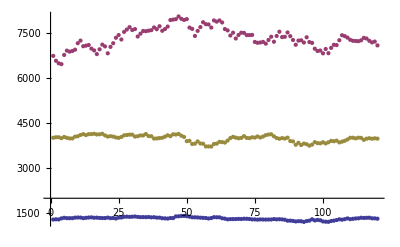

```mathematica
ListPlot[{hedge,dax,d2}]
```

```mathematica
Export["c:\\outt.csv",Transpose[{hedge,dax,d2}]]
```

c:\outt.csv

```mathematica
hedge=Log[hedge];dax=Log[dax];d2=Log[d2];
```

```mathematica
hedge=Differences[hedge];
```

```mathematica
dax=Differences[dax];d2=Differences[d2];
```

```mathematica
w=Transpose[{hedge,dax,d2}];
```

```mathematica
w=Sort[w,#1[[1]]<#2[[1]]&];
```

```mathematica
hedge=Transpose[w][[1]];
dax=Transpose[w][[2]];
d2=Transpose[w][[3]];
```

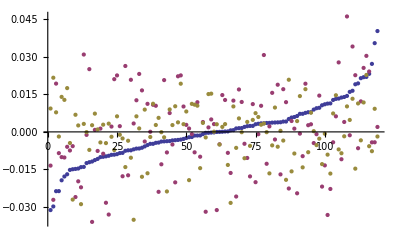

```mathematica
ListPlot[Transpose[w][[1;;3]],PlotRange->All]
```

```mathematica
min0=Min[Transpose[w][[1]]];wN=Length[hedge];nn=wN;
max0=Max[Transpose[w][[1]]];
min1=Min[Transpose[w][[2]]];
max1=Max[Transpose[w][[2]]];
```

```mathematica
U={};sdax=Sort[dax];AppendTo[U,{max0,max1,1}];

For[i=1,i≤nn,i++,
AppendTo[U,{hedge[[i]],max1,(i-1)/nn}];
AppendTo[U,{max0,sdax[[i]],(i-1)/nn}];
AppendTo[U,{hedge[[i]],min1,0}];
AppendTo[U,{min0,sdax[[i]],0}];
]
```

```mathematica
F={};For[i=1,i≤wN,i++,
AppendTo[F,{w[[i,1]],w[[i,2]],Length[Select[w,#[[1]]<w[[i,1]]  && #[[2]]<w[[i,2]]&]]/wN}];
]
```

```mathematica
W=Join[F,U];
```

```mathematica
ListPointPlot3D[W]
```

-Graphics3D-

```mathematica
hedgeI=Table[{hedge[[i]],(i-1)/(nn-1)},{i,nn}];d2I=Table[{Sort[d2][[i]],(i-1)/(nn-1)},{i,nn}];
daxI=Table[{sdax[[i]],(i-1)/(nn-1)},{i,nn}];W=F;Co=Table[{Select[hedgeI,#[[1]]==W[[i,1]]&][[1,2]],Select[daxI,#[[1]]==W[[i,2]]&][[1,2]],W[[i,3]]},{i,Length[W]}];AppendTo[Co,{1,0,0}];AppendTo[Co,{0,1,0}];AppendTo[Co,{1,1,1}];
```

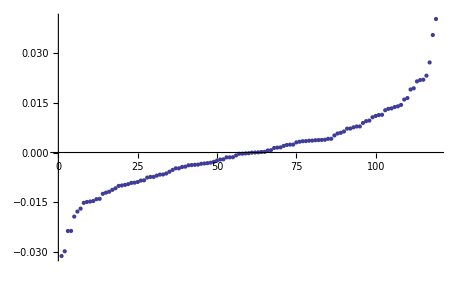
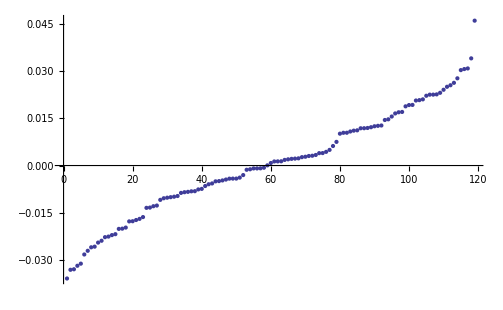
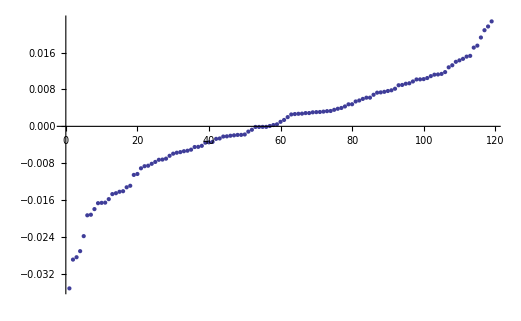

```mathematica
{ListPlot[Sort[hedge]],ListPlot[Sort[dax]],ListPlot[Sort[d2]]}
```

```mathematica
ListPointPlot3D[Co]
```

-Graphics3D-

```mathematica
Show[ListPlot3D[Co,Mesh->All],ListPointPlot3D[Co,PlotStyle->Red]]
```

-Graphics3D-